## MATH355 - Calculus III Lab #5 Centroid of Triangle with Varying Density

### In this lab we will have Mathematica do the mathematics of finding the centroid of a triangle region with varying density. Initially, however, we will do the centroid of the triangle with constant density.

18 k

36 k

36 k

2

2

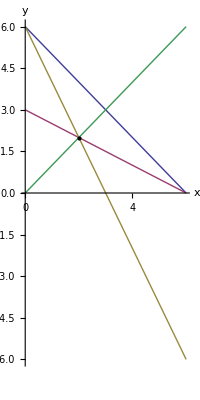

```mathematica
Clear[x,y,f,m,ρ]
f[x_]:=-x+6
m1[x_]:=-1/2 x+3
m2[x_]:=-2x+6
m3[x_]:=x
p1=Plot[{f[x],m1[x],m2[x],m3[x]},{x,0,6},AxesLabel->{x,y},AspectRatio->Automatic];
ρ[x_,y_]:=k
mass=∫_0^6 ∫_0^f[x] ρ[x,y]ⅆyⅆx
momentx=∫_0^6 ∫_0^f[x] ρ[x,y]y ⅆyⅆx
momenty=∫_0^6 ∫_0^f[x] ρ[x,y]x ⅆyⅆx
xbar=momenty/mass
ybar=momentx/mass
centroid=Graphics[{PointSize[Large],Point[{xbar,ybar}]}];
Show[p1,centroid]
```

### Next, let us vary the density by letting ρ( x, y ) = kx.

36 k

54 k

108 k

3

3/2

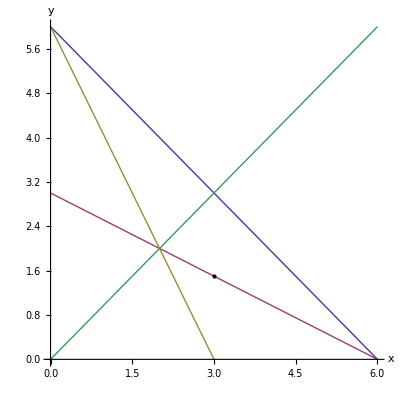

```mathematica
Clear[f,m,ρ,x,y]
f[x_]:=-x+6
m1[x_]:=-1/2 x+3
m2[x_]:=-2x+6
m3[x_]:=x
p1=Plot[{f[x],m1[x],m2[x],m3[x]},{x,0,6},PlotRange->{{0,6},{0,6}},AxesLabel->{x,y},AspectRatio->Automatic];
ρ[x_,y_]:=k*x
mass=∫_0^6 ∫_0^f[x] ρ[x,y]  ⅆyⅆx
momentx=∫_0^6 ∫_0^f[x] ρ[x,y]y  ⅆyⅆx
momenty=∫_0^6 ∫_0^f[x] ρ[x,y]x  ⅆyⅆx
xbar=momenty/mass
ybar=momentx/mass
centroid=Graphics[{PointSize[Large],Point[{xbar,ybar}]}];
Show[p1,centroid]
```

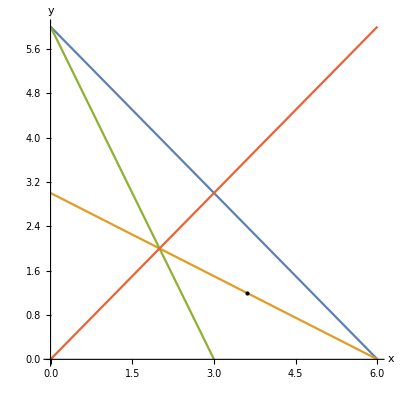
### Exercises 1. Vary the density by letting ρ( x, y ) = kx^2. -Graphics- 2. Generalize your result to ρ( x, y ) = kx^n. -Graphics- 3. Prove your generalization by having Mathematica find the limit as n→∞. view bellow

```mathematica
(*
part 1
*)
Clear[f,m,ρ,x,y]
f[x_]:=-x+6
m1[x_]:=-1/2 x+3
m2[x_]:=-2x+6
m3[x_]:=x
p1=Plot[{f[x],m1[x],m2[x],m3[x]},{x,0,6},PlotRange->{{0,6},{0,6}},AxesLabel->{x,y},AspectRatio->Automatic];
ρ[x_,y_]:=k*x*x
mass=∫_0^6 ∫_0^f[x] ρ[x,y]  ⅆyⅆx
momentx=∫_0^6 ∫_0^f[x] ρ[x,y]y  ⅆyⅆx
momenty=∫_0^6 ∫_0^f[x] ρ[x,y]x  ⅆyⅆx
xbar=momenty/mass
ybar=momentx/mass
centroid=Graphics[{PointSize[Large],Point[{xbar,ybar}]}];
Show[p1,centroid]
```

108 k

(648 k)/5

(1944 k)/5

18/5

6/5

-Graphics-

```mathematica
(*
part 2
*)
Clear[f,m,ρ,x,y]
f[x_]:=-x+6
m1[x_]:=-1/2 x+3
m2[x_]:=-2x+6
m3[x_]:=x
p1=Plot[{f[x],m1[x],m2[x],m3[x]},{x,0,6},PlotRange->{{0,6},{0,6}},AxesLabel->{x,y},AspectRatio->Automatic];
ρ[x_,y_]:=k*x^n
mass=∫_0^6 ∫_0^f[x] ρ[x,y]  ⅆyⅆx
momentx=∫_0^6 ∫_0^f[x] ρ[x,y]y  ⅆyⅆx
momenty=∫_0^6 ∫_0^f[x] ρ[x,y]x  ⅆyⅆx
xbar=momenty/mass
ybar=momentx/mass
centroid=Graphics[{PointSize[Large],Point[{xbar,ybar}]}];
Show[p1,centroid]
```

ConditionalExpression[(6^(2+n) k)/(2+3 n+n^2),Re[n]>-1]

ConditionalExpression[(6^(3+n) k)/(6+11 n+6 n^2+n^3),Re[n]>-1]

ConditionalExpression[(6^(3+n) k)/(6+5 n+n^2),Re[n]>-2]

ConditionalExpression[(6 (2+3 n+n^2))/(6+5 n+n^2),Re[n]>-1]

ConditionalExpression[(6 (2+3 n+n^2))/(6+11 n+6 n^2+n^3),Re[n]>-1]

-Graphics-

```mathematica
(*
part 3
*)
Clear[f,m,ρ,x,y]
f[x_]:=-x+6
m1[x_]:=-1/2 x+3
m2[x_]:=-2x+6
m3[x_]:=x
p1=Plot[{f[x],m1[x],m2[x],m3[x]},{x,0,6},PlotRange->{{0,6},{0,6}},AxesLabel->{x,y},AspectRatio->Automatic];
ρ[x_,y_]:=k*x^n
mass=∫_0^6 ∫_0^f[x] ρ[x,y]  ⅆyⅆx
momentx=∫_0^6 ∫_0^f[x] ρ[x,y]y  ⅆyⅆx
momenty=∫_0^6 ∫_0^f[x] ρ[x,y]x  ⅆyⅆx
xbar=momenty/mass
ybar=momentx/mass
centroid=Graphics[{PointSize[Large],Point[{xbar,ybar}]}];
Show[p1,centroid]
Limit[(6^(3+n) k)/(6+11 n+6 n^2+n^3)/((6^(2+n) k)/(2+3 n+n^2)), n ->  Infinity]
Limit[(6^(3+n) k)/(6+5 n+n^2)/((6^(2+n) k)/(2+3 n+n^2)), n -> Infinity]
```

ConditionalExpression[(6^(2+n) k)/(2+3 n+n^2),Re[n]>-1]

ConditionalExpression[(6^(3+n) k)/(6+11 n+6 n^2+n^3),Re[n]>-1]

ConditionalExpression[(6^(3+n) k)/(6+5 n+n^2),Re[n]>-2]

ConditionalExpression[(6 (2+3 n+n^2))/(6+5 n+n^2),Re[n]>-1]

ConditionalExpression[(6 (2+3 n+n^2))/(6+11 n+6 n^2+n^3),Re[n]>-1]

-Graphics-

0

6